# Projecto TAFC

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]
```

### Definição de variáveis

```mathematica
l[i_,t_]:=√((x[t]-xtoe[i])^2+(y[t]-ytoe[i])^2)
F[i_,t_]:=k(l0-l[i,t])
```

### Fase 1 - Suporte único

```mathematica
f1x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]
f1y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

### Fase 2 -Duplo suporte

```mathematica
f2x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]+F[2,t]/m(x[t]-xtoe[2])/l[2,t]
f2y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]+F[2,t]/m(y[t]-ytoe[2])/l[2,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (x[t]-xtoe[2]) (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)) (y[t]-ytoe[2]))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

### Runge-Kutta 4^aordem

```mathematica
(*parametros numéricos e condições iniciais*)

params={k->14000,g->9.81,m->80,l0->1.0,Energy->800};
l0=l0/.params;
f1nx=f1x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2nx=f2x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f1ny=f1y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2ny=f2y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
(*Posição Inicial do CoM no eixo x*)
xn[0]=0;
(*Inicialização do calcanhar*)
xtoe[1]=0;
ytoe[1]=0;

(*Ângulo de Touchdown, ângulo de ataque, é o ângulo ao qual chegada a posição l0 Sin [θcrit] troca-se de single para double support*)
θcrit=1.1100294042683936;
(*começamos com single support*)
cases=1;
(*Parametros numéricos*)
Nmax=10000;
Δt =0.001;

(*Parametros a mudar*)

(*Altura inicial da perna*)
yn[0]=0.9687135280718239;

(*Velocidade, obtida da energia*)
v=√(2/m(Energy-m g yn[0] - k/2(l0-yn[0])^2))/.params
(*ângulo da velocidade*)
α0=0;
xn'[0]=v Cos[α0];
yn'[0]=v Sin[α0];

For[i=0;step=0;L1={0};stepMAX=1,i<=Nmax,i++,
If[Mod[i,IntegerPart[0.25Nmax]]==0,Print[N[i/Nmax 100]]];
(*Suporte Único*)
(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==1,
K1vx=f1nx;
K2vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K1vx,yn[i]->yn[i]+0.5Δt K1vx};
K3vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K2vx,yn[i]->yn[i]+0.5Δt K2vx};
K4vx=f1nx/.{xn[i]->xn[i]+ Δt K3vx,yn[i]->yn[i]+Δt K3vx};
xn'[i+1]=xn'[i]+Δt/6(K1vx+2K2vx+2K3vx+K4vx);

(*Vy*)
K1vy=f1ny;
K2vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K1vy,yn[i]->yn[i]+0.5Δt K1vy};
K3vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K2vy,yn[i]->yn[i]+0.5Δt K2vy};
K4vy=f1ny/.{xn[i]->xn[i]+ Δt K3vy,yn[i]->yn[i]+Δt K3vy};
yn'[i+1]=yn'[i]+Δt/6(K1vy+2K2vy+2K3vy+K4vy);


(*Runge kutta para as posições*)
(*X*)
K1x=xn'[i];
K2x=xn'[i]+0.5Δt K1x;
K3x=xn'[i]+0.5 Δt K2x;
K4x=xn'[i]+Δt K3x;

xn[i+1]=xn[i]+Δt/6(K1x+2K2x+2K3x+K4x);
(*Y*)
K1y=yn'[i];
K2y=yn'[i]+0.5Δt K1y;
K3y=yn'[i]+0.5 Δt K2y;
K4y=yn'[i]+Δt K3y;

yn[i+1]=yn[i]+Δt/6(K1y+2K2y+2K3y+K4y)];
(*Suporte Duplo*)

(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==2,
G1vx=f2nx;
G2vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G1vx,yn[i]->yn[i]+0.5Δt G1vx};
G3vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G2vx,yn[i]->yn[i]+0.5Δt G2vx};
G4vx=f2nx/.{xn[i]->xn[i]+ Δt G3vx,yn[i]->yn[i]+Δt G3vx};
xn'[i+1]=xn'[i]+Δt/6(G1vx+2G2vx+2G3vx+G4vx);

(*Vy*)
G1vy=f2ny;
G2vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G1vy,yn[i]->yn[i]+0.5Δt G1vy};
G3vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G2vy,yn[i]->yn[i]+0.5Δt G2vy};
G4vy=f2ny/.{xn[i]->xn[i]+ Δt G3vy,yn[i]->yn[i]+Δt G3vy};
yn'[i+1]=yn'[i]+Δt/6(G1vy+2G2vy+2G3vy+G4vy);

(*Runge kutta para as posições*)
(*X*)
G1x=xn'[i];
G2x=xn'[i]+0.5Δt G1x;
G3x=xn'[i]+0.5 Δt G2x;
G4x=xn'[i]+Δt G3x;

xn[i+1]=xn[i]+Δt/6(G1x+2G2x+2G3x+G4x);
(*Y*)
G1y=yn'[i];
G2y=yn'[i]+0.5Δt G1y;
G3y=yn'[i]+0.5 Δt G2y;
G4y=yn'[i]+Δt G3y;

yn[i+1]=yn[i]+Δt/6(G1y+2G2y+2G3y+G4y)];

(*transição single support para double support*)
If[cases==1 &&yn'[i]<0&& yn[i]<=l0 Sin[θcrit]&&yn[i-1]>l0 Sin[θcrit] && caso[i-1]≠2,

cases=2;
xtoe[2]=xn[i]+l0 Cos[θcrit];
ytoe[2]=0];

(*transição de double support para single support*)
If[cases==2 &&  √((xn[i]-xtoe[1])^2+(yn[i]-ytoe[1])^2)≥l0 (*||√((xn[i]-xtoe[2])^2+(yn[i]-ytoe[2])^2)≥l0*), 
xtoe[1]=xtoe[2];
ytoe[1]=ytoe[2];
cases=1];

caso[i]=cases;
xtoe1i[i]=xtoe[1];
xtoe2i[i]=xtoe[2];

If[(xn[i]-xtoe1i[i])>0&&(xn[i-1]-xtoe1i[i-1])<0&&i>10&&caso[i]==1 &&caso[i-1]!=2 ,
L1=Join[L1,{i}];
step=step+1];
If[step>=stepMAX ,
istepmax=i;
Break[]]
]
```

0.

0.906942

0.

```mathematica
nlinhas=15;
Rugo[xkezd_,ykezd_,xveg_,yveg_]:={
hx=xveg-xkezd;hy=yveg-ykezd;szel=l0/(3*20);veghossz= l0/3.5;
hossz=√(hx^2+hy^2);
dh=(hossz-2*veghossz)/nlinhas;
{xkezd,ykezd}}~Join~{{xkezd+hx*(dh+veghossz)/hossz,ykezd+hy*(dh+veghossz)/hossz}}~Join~Table[If[OddQ[i],{xkezd+hx*(i*dh+veghossz)/hossz+hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz-hx*szel/hossz},
{xkezd+hx*(i*dh+veghossz)/hossz-hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz+hx*szel/hossz}],{i,2,nlinhas-2}]~Join~{{xkezd+hx*((nlinhas-1)*dh+veghossz)/hossz,ykezd+hy*((nlinhas-1)*dh+veghossz)/hossz}}~Join~{{xveg,yveg}}
```

```mathematica
Nmax1= istepmax
COM=ListPlot[Table[{xn[i],yn[i]},{i,0,Nmax1}],PlotStyle->{Black,PointSize[0.0015]}];
chao=Graphics[{Thickness->0.005,Line[{{0,0},{xn[istepmax],0}}]}];
limite1=Graphics[{Dashed,PointSize[0.0025],Line[{{0,l0 Sin[θcrit]},{xn[istepmax],l0 Sin[θcrit]}}]}];
massas=Graphics[{Disk[{xn[0],yn[0]},0.015],Disk[{xn[264],yn[264]},0.015],Disk[{xn[395],yn[395]},0.015],Disk[{xn[659],yn[659]},0.015]}];
molas=Graphics[{Line[Rugo[0,0,xn[0],yn[0]]],Line[Rugo[xtoe1i[659],0,xn[659],yn[659]]],Gray,Line[Rugo[0,0,xn[264],yn[264]]],Line[Rugo[0,0,xn[395],yn[395]]],Line[Rugo[xn[264],yn[264],xtoe2i[264],0]],Line[Rugo[xn[395],yn[395],xtoe2i[395],0]]}];
arrow=Graphics[Arrow[{{-0.2,yn[0]},{0,yn[0]}}]];
limite11=Graphics[Line[{{xn[659],l0 Sin[θcrit]},{xn[659]+0.1,l0 Sin[θcrit]}}]];
limite12=Graphics[Line[{{xn[659],0},{xn[659]+0.1,0}}]];
limite13=Graphics[Line[{{xn[659]+0.1,0},{xn[659]+0.1,l0 Sin[θcrit]}}]];
limite14=Graphics[Line[{{xn[659]+0.1,l0 Sin[θcrit]/2},{xn[659]+0.15,l0 Sin[θcrit]/2}}]];
limite2=Graphics[Line[{{-0.1,yn[0]},{-0.1,0}}]];
limite21=Graphics[Line[{{-0.1,0},{0,0}}]];
limite22=Graphics[Line[{{xn[0]-0.1,yn[0] 1/2},{xn[0]-0.15,yn[0] 1/2}}]];
limite3=Graphics[{Line[{{0,1.1},{xn[264],1.1}}],Line[{{0,1.075},{0,1.125}}],Line[{{xn[264],1.075},{xn[264],1.125}}]}];
limite4=Graphics[{Line[{{xn[264],1.1},{xn[395],1.1}}],Line[{{xn[264],1.075},{xn[264],1.125}}],Line[{{xn[395],1.075},{xn[395],1.125}}]}];
limite5=Graphics[{Line[{{xn[395],1.1},{xn[659],1.1}}],Line[{{xn[395],1.075},{xn[395],1.125}}],Line[{{xn[659],1.075},{xn[659],1.125}}]}];
arco=Graphics[Circle[{xtoe2i[264],0},0.1,{π-θcrit,π}]];
labels=Graphics[{Text["Single Sup.",{xn[264]/2,1.15}],Text["Double Sup.",{(xn[395]+xn[264])/2,1.15}],Text["Single Sup.",{(xn[395]+xn[659])/2,1.15}],FontSize->Large,Text["l_0sin(α_TD)",{xn[659]+0.32,l0 Sin[θcrit]/2}],Text["y_0",{-0.2,yn[0]/2}],Text["β=0.ba",{0.015,yn[0]+0.05}],Text["v⃗",{-0.23,yn[0]}],Text["α_TD",{xtoe2i[264]-0.135,0.08}],Text["l_0",{xn[264],yn[0]/2-0.05}]}];
```

659

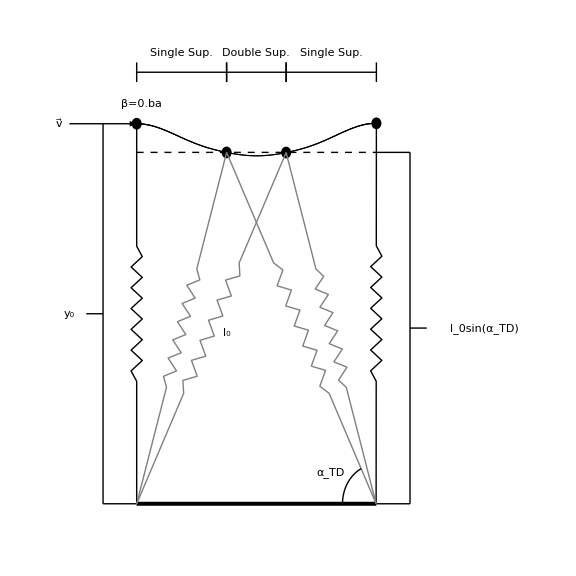

```mathematica
imagem1=Show[COM,chao,limite1,limite11,limite12,limite13,limite14,limite2,limite21,limite22,limite3,limite4,limite5,massas,molas,arrow,arco,labels,PlotRange->{{-0.25,1.15},{-0.05,1.15}},Axes->False,AspectRatio->1,ImageSize->Large]
```

```mathematica
SetDirectory["/home/nteixeira/S1_2018_2019/PMEFT/TAFC/desenhos"]
```

/home/nteixeira/Desktop/S1_2018_2019/PMEFT/TAFC/desenhos

```mathematica
Export["Seyfarth2006.png",imagem1,Resolution->750]
```

Seyfarth2006.png

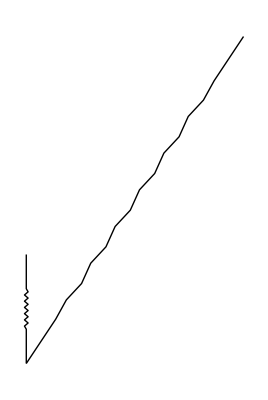

```mathematica
Graphics[{Line[Rugo[0,0,0,1]],Line[Rugo[0,0,2,3]]}]
```

```mathematica
Manipulate[Show[Evaluate[If[caso[j]==2, Graphics[Line[Rugo[xtoe2i[j],0,xn[j],yn[j]]]]]]/.Null->Sequence[],Graphics[Line[Rugo[xtoe1i[j],0,xn[j],yn[j]]]],ListPlot[Table[{xn[i],yn[i]},{i,0,j}]],PlotRange->All(*{{0, Max[Table[{xn[i]},{i,0,Nmax1}]]},{0,1.0}}*)],{j,0,Nmax1,1}]
istepmax
```

659